## Preliminaries and Inputs:

```mathematica
DocInnerProd[A_,B_]:=Conjugate[Flatten[A]].Flatten[B]
```

```mathematica
comm[A_,B_]:=A.B-B.A
```

```mathematica
NPrec=20;
```

```mathematica
H={{-2,-1,-1,0,-1,0,0,0},{-1,0,0,-1,0,-1,0,0},{-1,0,2,-1,0,0,-1,0},{0,-1,-1,0,0,0,0,-1},{-1,0,0,0,0,-1,-1,0},{0,-1,0,0,-1,2,0,-1},{0,0,-1,0,-1,0,0,-1},{0,0,0,-1,0,-1,-1,-2}};Operator={{3,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-3}};
```

```mathematica
H4={{-3,-1,-1,0,-1,0,0,0,-1,0,0,0,0,0,0,0},{-1,-1,0,-1,0,-1,0,0,0,-1,0,0,0,0,0,0},{-1,0,1,-1,0,0,-1,0,0,0,-1,0,0,0,0,0},{0,-1,-1,-1,0,0,0,-1,0,0,0,-1,0,0,0,0},{-1,0,0,0,1,-1,-1,0,0,0,0,0,-1,0,0,0},{0,-1,0,0,-1,3,0,-1,0,0,0,0,0,-1,0,0},{0,0,-1,0,-1,0,1,-1,0,0,0,0,0,0,-1,0},{0,0,0,-1,0,-1,-1,-1,0,0,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,0,-1,-1,-1,0,-1,0,0,0},{0,-1,0,0,0,0,0,0,-1,1,0,-1,0,-1,0,0},{0,0,-1,0,0,0,0,0,-1,0,3,-1,0,0,-1,0},{0,0,0,-1,0,0,0,0,0,-1,-1,1,0,0,0,-1},{0,0,0,0,-1,0,0,0,-1,0,0,0,-1,-1,-1,0},{0,0,0,0,0,-1,0,0,0,-1,0,0,-1,1,0,-1},{0,0,0,0,0,0,-1,0,0,0,-1,0,-1,0,-1,-1},{0,0,0,0,0,0,0,-1,0,0,0,-1,0,-1,-1,-3}};
```

```mathematica
H5={{-4,-1,-1,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-1,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,-1,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,-1,-2,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,-1,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,-1,2,0,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,-1,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,-1,-1,-2,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,-1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,-1,2,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,-1,0,4,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,-1,-1,2,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0,-1,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0,0,-1,0,0,-1,2,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0,0,0,-1,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1,0,0,0,-1,0,-1,-1,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-1,-1,0,-1,0,0,0,-1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,-1,0,0,0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,2,-1,0,0,-1,0,0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,2,-1,-1,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,4,0,-1,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,2,-1,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-2,-1,-1,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,-1,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,2,-1,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,-1,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,-2,-1,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,-1,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,-1,0,-1,0,-2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,-1,0,-1,-1,-4}};
```

```mathematica
Op={{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}};
```

```mathematica
σx={{0,1,1,0,1,0,0,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,0,0,1,0,1,1,0}};
```

```mathematica
σx4={{0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0},{0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0}};
```

```mathematica
{{0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0},{0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0}};
```

```mathematica
σx5={{0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0}};
```

```mathematica
σy={{0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0},{ⅈ,0,0,-ⅈ,0,-ⅈ,0,0},{ⅈ,0,0,-ⅈ,0,0,-ⅈ,0},{0,ⅈ,ⅈ,0,0,0,0,-ⅈ},{ⅈ,0,0,0,0,-ⅈ,-ⅈ,0},{0,ⅈ,0,0,ⅈ,0,0,-ⅈ},{0,0,ⅈ,0,ⅈ,0,0,-ⅈ},{0,0,0,ⅈ,0,ⅈ,ⅈ,0}};
```

```mathematica
σy4={{0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0},{ⅈ,0,0,-ⅈ,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0},{ⅈ,0,0,-ⅈ,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0},{0,ⅈ,ⅈ,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0},{ⅈ,0,0,0,0,-ⅈ,-ⅈ,0,0,0,0,0,-ⅈ,0,0,0},{0,ⅈ,0,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,-ⅈ,0,0},{0,0,ⅈ,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,0,-ⅈ,0},{0,0,0,ⅈ,0,ⅈ,ⅈ,0,0,0,0,0,0,0,0,-ⅈ},{ⅈ,0,0,0,0,0,0,0,0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0},{0,ⅈ,0,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,-ⅈ,0,0},{0,0,ⅈ,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,0,-ⅈ,0},{0,0,0,ⅈ,0,0,0,0,0,ⅈ,ⅈ,0,0,0,0,-ⅈ},{0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,-ⅈ,-ⅈ,0},{0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,ⅈ,0,0,-ⅈ},{0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,ⅈ,0,0,-ⅈ},{0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,ⅈ,ⅈ,0}};
```

```mathematica
σy5={{0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{ⅈ,0,0,-ⅈ,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{ⅈ,0,0,-ⅈ,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,ⅈ,ⅈ,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{ⅈ,0,0,0,0,-ⅈ,-ⅈ,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0},{0,ⅈ,0,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0},{0,0,ⅈ,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,ⅈ,0,ⅈ,ⅈ,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0},{ⅈ,0,0,0,0,0,0,0,0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0},{0,ⅈ,0,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0},{0,0,ⅈ,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0},{0,0,0,ⅈ,0,0,0,0,0,ⅈ,ⅈ,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0},{0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,-ⅈ,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0},{0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0},{0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0},{0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,ⅈ,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ},{ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0},{0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0},{0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0},{0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,ⅈ,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0},{0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,-ⅈ,-ⅈ,0,0,0,0,0,-ⅈ,0,0,0},{0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,-ⅈ,0,0},{0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,ⅈ,0,0,-ⅈ,0,0,0,0,0,0,-ⅈ,0},{0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,ⅈ,ⅈ,0,0,0,0,0,0,0,0,-ⅈ},{0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,-ⅈ,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,ⅈ,0,0,-ⅈ,0,0,-ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,ⅈ,ⅈ,0,0,0,0,-ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,-ⅈ,-ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,ⅈ,0,0,-ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,ⅈ,0,0,-ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,ⅈ,ⅈ,0}};
```

```mathematica
σz={{3,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-3}};
```

```mathematica
σz4={{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4}};
```

```mathematica
{vals,vecs} = Eigensystem[H];
```

```mathematica
tMax=1000;
tPts=100;
Prec=40;
tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], Prec];
```

## Lanczos Orthog

```mathematica
(*Generate set with repeated actions of Liouvillian on state Op*)
InitialBasis[H_,Op_,n_,prec_]:=
Module[{B},B=N[NestList[comm[H,#]&,Op,n],prec]]
```

```mathematica
(*Generate Othogonal Basis*)
OrthoBasis[H_,Op_,n_,prec_]:=
Module[{B},B=Orthogonalize[InitialBasis[H,Op,n-1,prec],DocInnerProd, Method->"GramSchmidt",Tolerance->10^(-10)]]
```

```mathematica
(*Extract b_ns from the off-diagonals of the Louivillian in the Krylov Basis*)
LanczosOrthog[H_,Op_,nmax_,prec_]:=
Module[{B,a,b},
B=OrthoBasis[H,Op,nmax,prec];
a=Table[DocInnerProd[B[[n]],comm[H,B[[n]]]],{n,1,nmax-1}];
b=Table[DocInnerProd[B[[n-1]],comm[H,B[[n]]]],{n,2,nmax-1}];
{a,b}]
```

## Moments Method

```mathematica
MomentsMethod[ReturnAmplitude_, N_]:=Module[{},
nnn=N*2;
NNNn[t_] := Simplify[Series[ReturnAmplitude, {t, 0, nnn} ]];
μTab = Table[Factorial[j]SeriesCoefficient[ NNNn[t], j], {j, 0, nnn}];
MijR = Simplify[   Sum[Table[KroneckerDelta[i+j+1-mm]*μTab[[mm]], {i, 0, (nnn)/2}, {j, 0, (nnn)/2}], {mm, 1, Length[μTab]}]   ]; 
bProd = Table[Det[MijR[[1;;k, 1;;k]]      ]/Det[MijR[[1;;(k-1), 1;;(k-1)]]      ], {k, 2, nnn/2+1}];  
bTab = Table[If[j==1, Sqrt[- bProd[[j]]   ],  Sqrt[- bProd[[j]]/bProd[[j-1]]    ]   ], {j, 1, Length[bProd]}];    
aTab =Table[Simplify[-I(    Simplify[   Cofactor[MijR[[1;;k, 1;;k]], {k-1,k}]/Det[MijR[[1;;k-1, 1;;k-1]]]   ] -    If[k > 2, Simplify[   Cofactor[MijR[[1;;k-1, 1;;k-1]], {k-2,k-1}]/Det[MijR[[1;;k-2, 1;;k-2]]]   ]  , 0])   ]  , {k, 2, Length[bTab]}   ]; 
{Re[aTab], Re[bTab]} 
]
```

```mathematica
MomentsMethod2[ReturnAmplitude_, N_]:=Module[{},
nnn=N*2;
NNNn[t_] := Series[ReturnAmplitude, {t, 0, nnn} ];
μTab = Table[Factorial[j]SeriesCoefficient[ NNNn[t], j], {j, 0, nnn}];

Print[Table[Precision[μTab[[i]]],{i,1,Length[μTab]}]];

MijR =  Sum[Table[KroneckerDelta[i+j+1-mm]*μTab[[mm]], {i, 0, (nnn)/2}, {j, 0, (nnn)/2}], {mm, 1, Length[μTab]}]   ; 
bProd = Table[Det[MijR[[1;;k, 1;;k]]      ]/Det[MijR[[1;;(k-1), 1;;(k-1)]]      ], {k, 2, nnn/2+1}];  

Print[Table[Precision[bProd[[i]]],{i,1,Length[bProd]}]];

bTab = Table[If[j==1, Sqrt[- bProd[[j]]   ],  Sqrt[- bProd[[j]]/bProd[[j-1]]    ]   ], {j, 1, Length[bProd]}];    
aTab=Table[Simplify[-I(    Simplify[   Cofactor[MijR[[1;;k, 1;;k]], {k-1,k}]/Det[MijR[[1;;k-1, 1;;k-1]]]   ] -    If[k > 2,   Cofactor[MijR[[1;;k-1, 1;;k-1]], {k-2,k-1}]/Det[MijR[[1;;k-2, 1;;k-2]]]    , 0])   ]  , {k, 2, Length[bTab]}   ]; 
{Re[aTab], Re[bTab]} 
]
```

```mathematica
MomentsMethod3[ReturnAmplitude_, N_]:=Module[{count},
nnn=N*2;
NNNn[t_] := Series[ReturnAmplitude, {t, 0, nnn} ];
μTab = Table[Factorial[j]SeriesCoefficient[ NNNn[t], j], {j, 0, nnn}];

MijR =  Sum[Table[KroneckerDelta[i+j+1-mm]*μTab[[mm]], {i, 0, (nnn)/2}, {j, 0, (nnn)/2}], {mm, 1, Length[μTab]}]   ;

bProd=ConstantArray[0,nnn/2+1];

Do[bProd[[k-1]]=Det[MijR[[1;;k, 1;;k]] ]/Det[MijR[[1;;(k-1), 1;;(k-1)]] ];
If[Abs[bProd[[k-1]]]<=10^(-10),count=k-1;Break[]], {k,2,nnn/2+1}];

bProd=bProd[[;;count]];

Print[Table[bProd[[i]],{i,1,Length[bProd]}]];
Print[Table[Precision[bProd[[i]]],{i,1,Length[bProd]}]];

bTab = Table[If[j==1, Sqrt[- bProd[[j]]   ],  Sqrt[- bProd[[j]]/bProd[[j-1]]    ]   ], {j, 1, Length[bProd]}];    
aTab=Table[Simplify[-I( Simplify[   Cofactor[MijR[[1;;k, 1;;k]], {k-1,k}]/Det[MijR[[1;;k-1, 1;;k-1]]] ] - If[k > 2, Cofactor[MijR[[1;;k-1, 1;;k-1]], {k-2,k-1}]/Det[MijR[[1;;k-2, 1;;k-2]]] , 0]) ]  , {k, 2, Length[bTab]}   ]; 
{Re[aTab], Re[bTab]}
]
```

```mathematica
nProd={1,2,3,4,5,6,7,8,9};
```

```mathematica
nProd[[;;3]]
```

{1,2,3}

```mathematica
bTab = Table[If[j==1, Sqrt[- nProd[[j]]   ],  Sqrt[- nProd[[j]]/nProd[[j-1]]    ]   ], {j, 1, Length[nProd]}];
```

```mathematica
While
```

```mathematica
bs=Bs[[1;;-1-LengthWhile[Reverse@Bs,#==0&]]]
```

## Testing with random return amplitudes

```mathematica
RandomInteger[{1,100}]
```

6

```mathematica
RetAmpNice=Sum[Exp[RandomInteger[{1,100}]*I*t],{i,1,30}]
```

ⅇ^(4 ⅈ t)+2 ⅇ^(7 ⅈ t)+ⅇ^(12 ⅈ t)+ⅇ^(21 ⅈ t)+ⅇ^(22 ⅈ t)+ⅇ^(24 ⅈ t)+ⅇ^(34 ⅈ t)+ⅇ^(39 ⅈ t)+2 ⅇ^(51 ⅈ t)+2 ⅇ^(53 ⅈ t)+3 ⅇ^(60 ⅈ t)+ⅇ^(62 ⅈ t)+ⅇ^(71 ⅈ t)+ⅇ^(72 ⅈ t)+ⅇ^(73 ⅈ t)+ⅇ^(75 ⅈ t)+ⅇ^(77 ⅈ t)+ⅇ^(78 ⅈ t)+ⅇ^(81 ⅈ t)+ⅇ^(82 ⅈ t)+2 ⅇ^(87 ⅈ t)+ⅇ^(91 ⅈ t)+ⅇ^(96 ⅈ t)+ⅇ^(99 ⅈ t)

```mathematica
MomentsMethod[RetAmpNice,10][[2]]
```

{√(237223/10),(4 √(6963026965595/3))/237223,(3 √125759503231981362777400710)/1392605393119,(43 √112032700706985923451190227452345127481)/17671066637999036459,(2 √2349695833171423396591798142997127081956015160540529047523010)/148748859246673805040259920751,(18 √1053775635339488796086100381072762489496912174206840382915250199568725203273629371)/22161422409733011511289044070841887076065,(280 √29341861155285716404628666762398417904261778704301698884619545987943930210021521373586519566645613898943)/63758342525019880731105547046881627682788637847842589,(9 √78570263433982671558563663607657427447637179332993850231278707351703217922287924246686583874532534767845866617444288242700289514831)/105920497747109043348960117435865637067172066157490232856336851376,(16 √2105390448010263633781908474843592924413981638502965985497612267558842684977259539290381025136794545177944564350554047779276405294191213696159661066576806760645)/33272463315448626480505035758439350212749297217735405373553535216154728171355033,(2 √77547463636132916412050089256988498834170594218206159316041304349946976631801189769126388383279714847541533209858354354244008294266939486510183252747273011604833134929641131153717808592536794)/21202221090131183584920120157663981490189159931294822721304859048611579366915543450203509939313}

```mathematica
RetAmpNiceN=Sum[Exp[N[RandomInteger[{1,100}],20]*I*t],{i,1,50}]
```

ⅇ^(1. ⅈ t)+ⅇ^(4. ⅈ t)+2 ⅇ^(8. ⅈ t)+2 ⅇ^(9. ⅈ t)+ⅇ^(10. ⅈ t)+ⅇ^(11. ⅈ t)+3 ⅇ^(12. ⅈ t)+ⅇ^(13. ⅈ t)+ⅇ^(15. ⅈ t)+ⅇ^(17. ⅈ t)+ⅇ^(18. ⅈ t)+3 ⅇ^(24. ⅈ t)+ⅇ^(25. ⅈ t)+ⅇ^(27. ⅈ t)+2 ⅇ^(29. ⅈ t)+ⅇ^(32. ⅈ t)+ⅇ^(36. ⅈ t)+3 ⅇ^(40. ⅈ t)+ⅇ^(41. ⅈ t)+ⅇ^(45. ⅈ t)+ⅇ^(51. ⅈ t)+ⅇ^(63. ⅈ t)+ⅇ^(64. ⅈ t)+ⅇ^(67. ⅈ t)+ⅇ^(68. ⅈ t)+ⅇ^(69. ⅈ t)+ⅇ^(71. ⅈ t)+ⅇ^(76. ⅈ t)+ⅇ^(77. ⅈ t)+ⅇ^(78. ⅈ t)+ⅇ^(80. ⅈ t)+2 ⅇ^(81. ⅈ t)+ⅇ^(82. ⅈ t)+ⅇ^(85. ⅈ t)+ⅇ^(86. ⅈ t)+2 ⅇ^(90. ⅈ t)+ⅇ^(96. ⅈ t)+ⅇ^(97. ⅈ t)+ⅇ^(99. ⅈ t)

```mathematica
MomentsMethod[RetAmpNiceN,50][[2]]
```

{218.46024810019785382,21.9286530599846619,27.49538791992083306,23.8658942666569366,26.74153063248082,23.6515333763596384,24.0055232212166315,23.731574244087637,25.2723679185856528,25.4344073747408197,23.3657880469150043,24.2886191613291299,21.3001703539358367,22.6993430078525201,21.5166198098135053,25.5364397206563574,20.4616084959994051,22.2249113866666154,22.6240787788189015,20.4590789848553908,62.353817947194295,58.0830066390775113,0,0,15.5506074081185628,0,0,47.865758548035221,0,0,0,0,0,0,0,2.4097837864832499,1079.1644644892114,0,0,0,4345.7679414018307,0,54116.941206111622,0,0,0,5.7269424318980224,53319.884703129695,0.027375910279872215,53211.093120799981}

```mathematica
RetAmpRan=Sum[Exp[RandomReal[]*I*t],{i,1,40}]
```

ⅇ^((0.+0.00756276 ⅈ) t)+ⅇ^((0.+0.0140025 ⅈ) t)+ⅇ^((0.+0.0377556 ⅈ) t)+ⅇ^((0.+0.0918491 ⅈ) t)+ⅇ^((0.+0.117854 ⅈ) t)+ⅇ^((0.+0.178727 ⅈ) t)+ⅇ^((0.+0.205888 ⅈ) t)+ⅇ^((0.+0.237037 ⅈ) t)+ⅇ^((0.+0.252338 ⅈ) t)+ⅇ^((0.+0.261954 ⅈ) t)+ⅇ^((0.+0.265863 ⅈ) t)+ⅇ^((0.+0.319399 ⅈ) t)+ⅇ^((0.+0.355069 ⅈ) t)+ⅇ^((0.+0.373577 ⅈ) t)+ⅇ^((0.+0.478188 ⅈ) t)+ⅇ^((0.+0.497091 ⅈ) t)+ⅇ^((0.+0.501274 ⅈ) t)+ⅇ^((0.+0.502461 ⅈ) t)+ⅇ^((0.+0.537516 ⅈ) t)+ⅇ^((0.+0.578734 ⅈ) t)+ⅇ^((0.+0.593195 ⅈ) t)+ⅇ^((0.+0.59961 ⅈ) t)+ⅇ^((0.+0.610249 ⅈ) t)+ⅇ^((0.+0.616742 ⅈ) t)+ⅇ^((0.+0.621251 ⅈ) t)+ⅇ^((0.+0.651938 ⅈ) t)+ⅇ^((0.+0.69736 ⅈ) t)+ⅇ^((0.+0.705986 ⅈ) t)+ⅇ^((0.+0.707243 ⅈ) t)+ⅇ^((0.+0.771036 ⅈ) t)+ⅇ^((0.+0.788954 ⅈ) t)+ⅇ^((0.+0.806178 ⅈ) t)+ⅇ^((0.+0.81223 ⅈ) t)+ⅇ^((0.+0.831059 ⅈ) t)+ⅇ^((0.+0.851241 ⅈ) t)+ⅇ^((0.+0.875714 ⅈ) t)+ⅇ^((0.+0.926821 ⅈ) t)+ⅇ^((0.+0.947686 ⅈ) t)+ⅇ^((0.+0.963792 ⅈ) t)+ⅇ^((0.+0.986026 ⅈ) t)

```mathematica
MomentsMethod[RetAmpRan,30][[2]]
```

$Aborted

## For TFIM using imported return amplitudes

### L=3

```mathematica
RetAmp3=ToExpression[Import["C:\\Users\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Return Amplitudes\\ReturnAmpNumL3TFIM.txt"]];
```

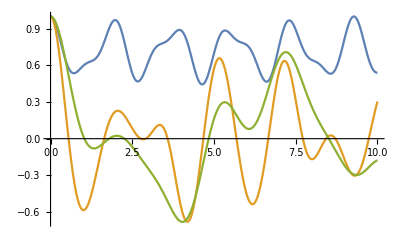

```mathematica
Plot[RetAmp3,{t,0,10}]
```

```mathematica
MomentsMethod[RetAmp3[[1]],10][[2]]
```

{2.309401076758503058036595122008,4.54606056566195196425286585064,2.816999089628490088604510581,3.8147504514818578827515577,0.2531762945816032028052437,2.7291201669793048504351,3.09485054724211517994×10^-15,0,62322.8693766975811,0}

```mathematica
MomentsMethod3[RetAmp3[[1]],10][[2]]
```

{-5.33333333333333333333333333333+0. ⅈ,110.22222222222222222222222222+0. ⅈ,-874.6666666666666666666666667,12728.430107526881720430108,-815.869918699186991869919,6076.6782006920415224913,-5.82030309257182904693×10^-26}

{30.9306,29.8179,28.2614,26.6074,24.9539,23.3088,21.673}

{2.309401076758503058036595122008,4.54606056566195196425286585064,2.816999089628490088604510581,3.8147504514818578827515577,0.2531762945816032028052437,2.7291201669793048504351,3.09485054724211517994×10^-15}

```mathematica
MomentsMethod3[RetAmp3[[1]],20][[2]]
```

{-5.33333333333333333333333333333+0. ⅈ,110.22222222222222222222222222+0. ⅈ,-874.6666666666666666666666667,12728.430107526881720430108,-815.869918699186991869919,6076.6782006920415224913,-5.82030309257182904693×10^-26}

{30.9306,29.8179,28.2614,26.6074,24.9539,23.3088,21.673}

{2.309401076758503058036595122008,4.54606056566195196425286585064,2.816999089628490088604510581,3.8147504514818578827515577,0.2531762945816032028052437,2.7291201669793048504351,3.09485054724211517994×10^-15}

### L=4

Questions:

Why is there a dramatic precision loss for p1,p2,p3 and not for c and cd?

```mathematica
RetAmp4=ToExpression[Import["C:\\Users\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Return Amplitudes\\ReturnAmpNumL4TFIM.txt"]];
```

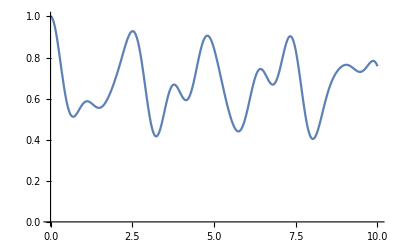

```mathematica
Plot[RetAmp4[[1]],{t,0,10}, PlotRange->{0,Automatic}]
```

```mathematica
bsL4=MomentsMethod2[RetAmp4[[5]],40][[2]]
```

{31.699,0.,31.3348,30.5014,31.176,30.5822,31.0577,30.5976,30.9637,30.5914,30.8861,30.575,30.82,30.5535,30.7625,30.5295,30.7117,30.5047,30.6661,30.4798,30.6249,30.4552,30.5872,30.4312,30.5525,30.4079,30.5204,30.3853,30.4905,30.3634,30.4625,30.3422,30.4362,30.3217,30.4114,30.3019,30.388,30.2827,30.3657,30.2641,30.3446,30.2461,30.3244,30.2287,30.3051,30.2118,30.2866,30.1954,30.2689,30.1794,30.2519,30.164,30.2355,30.1489,30.2197,30.1343,30.2044,30.1201,30.1897,30.1063,30.1755,30.0929,30.1617,30.0798,30.1483,30.067,30.1354,30.0546,30.1228,30.0425,30.1106,30.0307,30.0987,30.0192,30.0871,30.0079,30.0758,29.9969,30.0648,29.9862,30.0541}

{30.8403,30.1769,30.2004,30.2004,30.2004,30.2004,30.2004,30.2004,30.2004,30.1894,30.1663,30.142,30.1183,30.0954,30.0731,30.0516,30.0308,30.0107,29.9912,29.9723,29.954,29.9363,29.9191,29.9025,29.8863,29.8706,29.8553,29.8405,29.8261,29.8121,29.7985,29.7852,29.7723,29.7597,29.7475,29.7355,29.7239,29.7125,29.7014,29.6905}

{3.741657386773941385583748732317,4.67297920965603601736223560515,5.3351190710039967572787531396,4.83360417745158321031341897311,4.87632808124491884273617356548,4.69504213955349775228370232235,4.72572545557318834681907083779,4.86114215075725874090024938248,4.76587095137181456504842815738,5.04802042323437360150845061577,4.84677963888144670951240070017,4.11210827887202913012215093895,4.22804188682146799920824283897,4.25014514876115566889374118649,3.84888980843079628172784267078,4.09635936811042456636483411816,4.31159847171663441851672599015,4.33315417817414122121411369136,4.26375034150834657264206983405,3.830895877345142585361021576,3.3988029034302963094669119662,3.1458079600077372671785315337,3.5598075569329288662387556481,3.8901797506427187321172573657,3.0263378922943034142056363662,3.3767161282509170222565824162,2.8284575362341234660417616612,2.8881787201788047785713078556,3.6358139201112043980023660608,3.7280493737756438138091957272,2.3602506484283675189385711581,2.8105815532353341211247779907,3.4802032480286510298974917863,3.2402751704848552076009348032,1.9658430635335708905994526855,3.432199470725147374228774792,2.4070444300724894922552443714,2.7011006890994837261473168179,2.2351083826122113687614105864,2.5761325364595100063394992115}

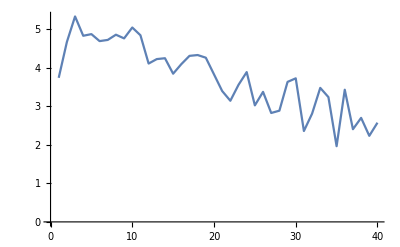

```mathematica
ListLinePlot[bsL4]
```

```mathematica
Table[Precision[bsL4[[i]]], {i ,1,Length[bsL4]}]
```

{31.1669,30.2707,29.8825,30.2004,30.2004,30.2004,30.2004,30.2004,30.2004,30.1949,30.1777,30.154,30.13,30.1067,30.0841,30.0623,30.0411,30.0206,30.0008,29.9816,29.9631,29.9451,29.9276,29.9107,29.8943,29.8784,29.8629,29.8479,29.8333,29.8191,29.8053,29.7918,29.7787,29.766,29.7536,29.7415,29.7297,29.7181,29.7069,29.6959}

```mathematica
bsL4=MomentsMethod2[RetAmp4[[1]],16][[2]];
Print[Precision[bsL4]];
Table[Precision[bsL4[[i]]], {i ,1,Length[bsL4]}]
```

5.98961

6.28198

7.97785

{31.2496,29.9887,28.4326,26.7605,25.0542,23.3417,21.6269,19.9123,18.1996,16.4895,14.7821,13.0775,11.3754,∞,7.97785,∞}

```mathematica
x=0.73801676778037380`13
```

0.7380167677804

```mathematica
Precision[x]
```

13.

```mathematica
Precision[Sqrt[x]]
```

13.301

{31.2496,29.9887,28.4326,26.7605,25.0542,23.3417,21.6269,19.9123,18.1996,16.4895,14.7821,13.0775,11.3754,∞,7.97785,∞}

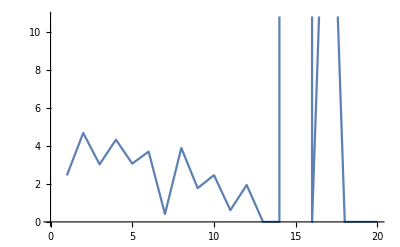

```mathematica
ListLinePlot[Out[118]]
```